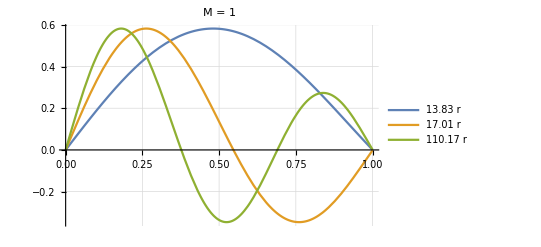

```mathematica
Plot[{BesselJ[1,3.83*r],BesselJ[1,7.01*r],BesselJ[1,10.17*r]},{r,0,1},
PlotLabel->"M = 1",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

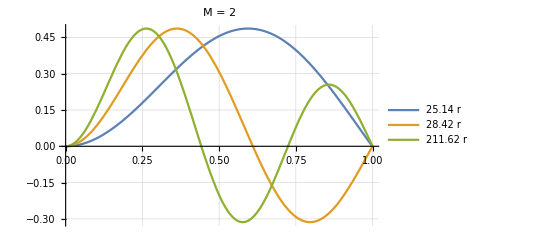

```mathematica
Plot[{BesselJ[2,5.14*r],BesselJ[2,8.42*r],BesselJ[2,11.62*r]},{r,0,1},
PlotLabel->"M = 2",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

```mathematica
RevolutionPlot3D[{BesselJ[1,3.83*r]*Sin[θ]},{r,0,1},{θ,0,π},PlotLabel->"ϕ_(1, 1)(r,θ)"]
```

-Graphics3D-

```mathematica
|
```

```mathematica
RevolutionPlot3D[BesselJ[2,7.01*r]*Sin[θ],{r,0,1},{θ,0,π},PlotLabel->"ϕ_(1, 2)(r,θ)"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[BesselJ[2,5.14*r]*Sin[2θ],{r,0,1},{θ,0,π},PlotLabel->"ϕ_(2, 1)(r,θ)"]
```

-Graphics3D-

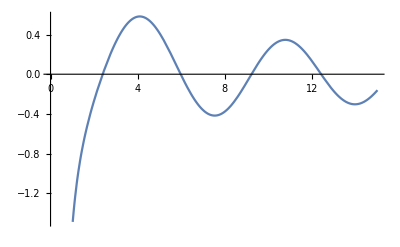

```mathematica
Plot[{BesselY[2,z]+BesselJ[2,z]},{z,0,15}]
```

```mathematica
P1 = FindRoot[BesselY[2,z]+BesselJ[2,z],{z,2.45}]
P2 = FindRoot[BesselY[2,z]+BesselJ[2,z],{z,5.95}]
P3 = FindRoot[BesselY[2,z]+BesselJ[2,z],{z,9.15}]
```

{z→2.39303}

{z→5.97098}

{z→9.22193}

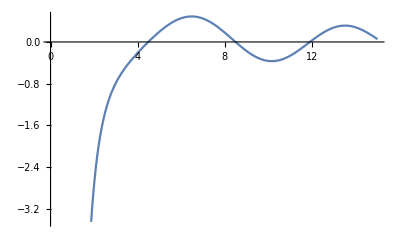

```mathematica
Plot[{BesselY[4,z]+BesselJ[4,z]},{z,0,15}]
```

```mathematica
P4 = FindRoot[BesselY[4,z]+BesselJ[4,z],{z,4.5}]
P5 = FindRoot[BesselY[4,z]+BesselJ[4,z],{z,8.5}]
P6 = FindRoot[BesselY[4,z]+BesselJ[4,z],{z,12}]
```

{z→4.48065}

{z→8.4872}

{z→11.901}

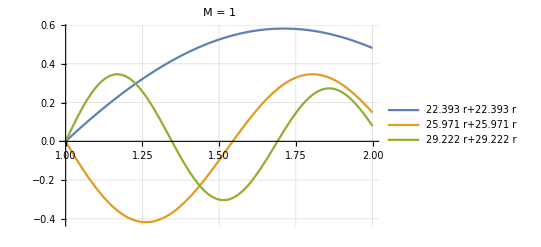

```mathematica
Plot[{BesselJ[2,2.393/1*r]+BesselY[2,2.393/1*r],BesselJ[2,5.971/1*r]+BesselY[2,5.971/1*r],BesselJ[2,9.222/1*r]+BesselY[2,9.222/1*r]},{r,1,2},
PlotLabel->"M = 1",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

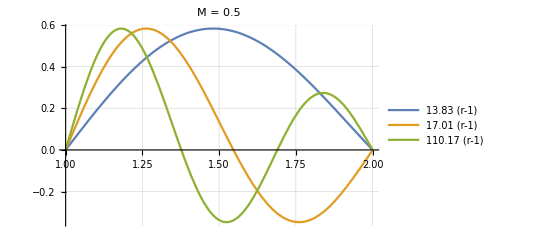

```mathematica
Plot[{BesselJ[1,3.83*(r-1)],BesselJ[1,7.01*(r-1)],BesselJ[1,10.17*(r-1)]},{r,1,2},
PlotLabel->"M = 0.5",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

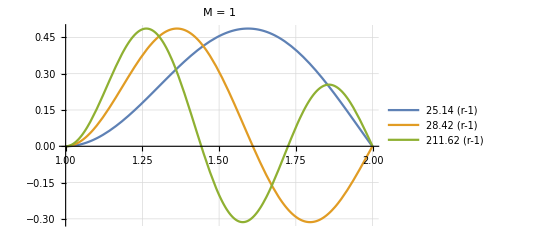

```mathematica
Plot[{BesselJ[2,5.14*(r-1)],BesselJ[2,8.42*(r-1)],BesselJ[2,11.62*(r-1)]},{r,1,2},
PlotLabel->"M = 1",
GridLines->Automatic,
PlotLegends->"Expressions",
BaseStyle->{FontSize->18},
PlotStyle->Thick]
```

```mathematica
RevolutionPlot3D[{BesselJ[1,3.83*(r-1)]*Sin[2θ]},{r,1,2},{θ,0,π/2},PlotLabel->"ϕ_(1, 1)(r,θ)"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[BesselJ[2,7.01*(r-1)]*Sin[2θ],{r,1,2},{θ,0,π/2},PlotLabel->"ϕ_(1, 2)(r,θ)"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[BesselJ[2,5.14*(r-1)]*Sin[4θ],{r,1,2},{θ,0,π/2},PlotLabel->"ϕ_(2, 1)(r,θ)"]
```

-Graphics3D-